```mathematica
Manipulate[ArrayPlot[Mean@CellularAutomaton[{976,{2,1},{1,1}},
SeedRandom[seed];Normal[Take[SparseArray[
Thread[If[Ceiling[d 80^2]==0,{},RandomSample[Tuples[Range[80],2],Ceiling[d 80^2]]]->1],50^2],w,w]],t],ImageSize->{500,338}],
{{seed,1234,"initial configuration"},1000,1500,1},
{{d,0.55,"initial density"},.0002,1,Appearance->"Labeled"},Delimiter,
{{t,5,"evolution steps"},0,600,1,Appearance->"Labeled"},Delimiter,
{{w,50,"grid size"},5,80,1,Appearance->"Labeled"},AutorunSequencing->{{4,5},{3,5},{2,5},{1,5}}]
```

```mathematica
Manipulate[ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors]
 ,2],2,3},SeedRandom[seed];Normal[SparseArray[Thread[RandomSample[Range[400],Round[d400]]->1],400]],50,400],ImageSize->{500,369},PlotRange->{{0,w},{0,w}},PlotLabel->Text[Style["Fraction of red cell: "<>ToString[d],"Output",Bold]],ColorRules->{0 -> Yellow, 1 -> Red}],
{{seed,1234,"Initial seeds "},1000,1500,1},
{{d,0.5,"Fraction of red cell "},0.002,1},Delimiter,

{{w,150,"zoom"},20,250,1}]
```

```mathematica
Manipulate[{r,y,b}={rVal,yVal,bVal}//If[Total[#]>1,#/Total@#,#]&;{rVal,yVal,bVal}={r,y,b};
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors]
 ,3],3,{{-110},{-90},{-5},{0},{40},{45},{60}}},SeedRandom[seed];

RandomChoice[{bVal,rVal, yVal}->{2,1,0},500],t],

ImageSize->{500,369},PlotRange->{{0,w},{0,w}},PlotLabel->Column[{Text[Style["Fraction of red cells: "<>ToString[rVal],"Output",Bold]],Text[Style["Fraction of yellow cells: "<>ToString[yVal],"Output",Bold]], Text[Style["Fraction of blue cells: "<>ToString[bVal],"Output",Bold]]}],ColorRules->{0 -> Yellow, 1 -> Red, 2-> Blue}],

{{seed,1200,"Initial seeds "},1000,1500,1},Delimiter,
{{rVal,.333,"Fraction of red"},0,1,Appearance->"Open"},{{yVal,.333,"Fraction of yellow"},0,1,Appearance->"Open"},{{bVal,.333,"Fraction of blue"},0,1,Appearance->"Open"},
{{t,60,"evolution steps"},0,600,1,Appearance->"Labeled"},Delimiter,
{{w,150,"zoom"},100,400,1}]
```

```mathematica
Manipulate[{r,y,b}={rVal,yVal,bVal}//If[Total[#]>1,#/Total@#,#]&;{rVal,yVal,bVal}={r,y,b};
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors]
 ,3],3,{{-10},{-9},{-2},{1},{4},{6},{10}}},SeedRandom[seed];

RandomChoice[{bVal,rVal, yVal}->{2,1,0},500],t],

ImageSize->{500,369},PlotRange->{{0,w},{0,w}},PlotLabel->Column[{Text[Style["Fraction of red cells: "<>ToString[rVal],"Output",Bold]],Text[Style["Fraction of yellow cells: "<>ToString[yVal],"Output",Bold]], Text[Style["Fraction of blue cells: "<>ToString[bVal],"Output",Bold]]}],ColorRules->{0 -> Yellow, 1 -> Red, 2-> Blue}],

{{seed,1200,"Initial seeds "},1000,1500,1},Delimiter,
{{rVal,.333,"Fraction of red"},0,1,Appearance->"Open"},{{yVal,.333,"Fraction of yellow"},0,1,Appearance->"Open"},{{bVal,.333,"Fraction of blue"},0,1,Appearance->"Open"},
{{t,60,"evolution steps"},0,600,1,Appearance->"Labeled"},Delimiter,
{{w,150,"zoom"},100,400,1}]
```

```mathematica
{FromDigits[Tuples[{2,1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors]
 ,3],3,3}
```

{291195106143185347887561556453855316541507000474753958044468138484313606114817262672190280461386347453536298325852152519560495982001746935735777135726934058828562129933081046908877087683079488340852212643646039570120256032158123095188756527272021588943088582316759357230115027658559192385266910639674091457047731283982258011154801710430444748607710477816386692080370938640826506211419912623559495073007244298971680159024676114254446474879524810586786466210969018527040269157445921024214858808444706348001472485815407313672044103741342197435526584571661604143411370367574153989301692668108793748887968662969408153560120425318055834120370897939587825542787375125509117063657003971847891389014151458797582248200109835729481016653685100898538010473547496930373832799667496316422105034954853400773195754020354185855596559693914227220239864360916770914472558249792893280964854381144019882743990342162912976993217908470266103989276733271656769672132114791241110298894327457991281200989719103290736541949377591052322040441278890672022934825099425605197,3,3}

```mathematica
Manipulate[{r,y,b}={rVal,yVal,bVal}//If[Total[#]>1,#/Total@#,#]&;{rVal,yVal,bVal}={r,y,b};
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors]
 ,3],3,3},SeedRandom[seed];

RandomChoice[{bVal,rVal, yVal}->{2,1,0},500],t],

ImageSize->{500,369},PlotRange->{{0,w},{0,w}},PlotLabel->Column[{Text[Style["Fraction of red cells: "<>ToString[rVal],"Output",Bold]],Text[Style["Fraction of yellow cells: "<>ToString[yVal],"Output",Bold]], Text[Style["Fraction of blue cells: "<>ToString[bVal],"Output",Bold]]}],ColorRules->{0 -> Yellow, 1 -> Red, 2-> Blue}],

{{seed,1200,"Initial seeds "},1000,1500,1},Delimiter,
{{rVal,.333,"Fraction of red"},0,1,Appearance->"Open"},{{yVal,.333,"Fraction of yellow"},0,1,Appearance->"Open"},{{bVal,.333,"Fraction of blue"},0,1,Appearance->"Open"},
{{t,60,"evolution steps"},0,600,1,Appearance->"Labeled"},Delimiter,
{{w,150,"zoom"},100,400,1}]
```

```mathematica
Manipulate[{r,y,b}={rVal,yVal,bVal}//If[Total[#]>1,#/Total@#,#]&;{rVal,yVal,bVal}={r,y,b};
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors]
 ,3],3,3},SeedRandom[seed];

RandomChoice[{bVal,rVal, yVal}->{2,1,0},500],t],

ImageSize->{500,369},PlotRange->{{0,w},{0,w}},PlotLabel->Column[{Text[Style["Fraction of red cells: "<>ToString[rVal],"Output",Bold]],Text[Style["Fraction of yellow cells: "<>ToString[yVal],"Output",Bold]], Text[Style["Fraction of blue cells: "<>ToString[bVal],"Output",Bold]]}],ColorRules->{0 -> Yellow, 1 -> Red, 2-> Blue}],

{{seed,1200,"Initial seeds "},1000,1500,1},Delimiter,
{{rVal,.333,"Fraction of red"},0,1,Appearance->"Open"},{{yVal,.333,"Fraction of yellow"},0,1,Appearance->"Open"},{{bVal,.333,"Fraction of blue"},0,1,Appearance->"Open"},
{{t,60,"evolution steps"},0,600,1,Appearance->"Labeled"},Delimiter,
{{w,150,"zoom"},100,400,1}]
```

static domain walls

```mathematica
Manipulate[{r,y,b}={rVal,yVal,bVal}//If[Total[#]>1,#/Total@#,#]&;{rVal,yVal,bVal}={r,y,b};
ArrayPlot[CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors]
 ,3],3,{{-10},{-9},{-2},{1},{4},{6},{10}}},SeedRandom[seed];

RandomChoice[{bVal,rVal, yVal}->{2,1,0},500],t],

ImageSize->{500,369},PlotRange->{{0,w},{0,w}},PlotLabel->Column[{Text[Style["Fraction of red cells: "<>ToString[rVal],"Output",Bold]],Text[Style["Fraction of yellow cells: "<>ToString[yVal],"Output",Bold]], Text[Style["Fraction of blue cells: "<>ToString[bVal],"Output",Bold]]}],ColorRules->{0 -> Yellow, 1 -> Red, 2-> Blue}],

{{seed,1200,"Initial seeds "},1000,1500,1},Delimiter,
{{rVal,.333,"Fraction of red"},0,1,Appearance->"Open"},{{yVal,.333,"Fraction of yellow"},0,1,Appearance->"Open"},{{bVal,.333,"Fraction of blue"},0,1,Appearance->"Open"},
{{t,60,"evolution steps"},0,600,1,Appearance->"Labeled"},Delimiter,
{{w,150,"zoom"},100,400,1}]
```

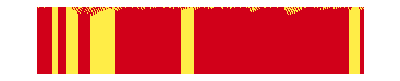

```mathematica
majrn[n_]:=FromDigits[If[Total[#]>n/2,1,0]&/@Tuples[{1,0},n],2]

BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[{majrn[5],2,{{-3},{-1},{0},{2},{4}}},RandomChoice[{.6,.4}->{1,0},300],60],ColorRules->{0->Hue[0.15,0.72,1],1->Hue[0.98,1,0.8200000000000001]},MeshStyle->Orange]]
```

```mathematica
data2D=ParallelTable[If[p==.5,Nothing,Mean/@Transpose[Table[Mean/@CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors],2],2,3},RandomChoice[{p,1-p }->{1,0},100],20],100]]],{p,.3,.7,.05}];

ListLinePlot[MapThread[Callout[#1,Row[{Style["p",Italic],"=",#2}]]&,{data2D,Cases[Range[.3,.7,.05],Except[0.5]]}],PlotRange->{0,1}]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Labeled[BlockRandom[SeedRandom[567];
ArrayPlot[CellularAutomaton[{4177065992,2,List/@#},RandomChoice[{.6,.4}->{1,0},300],100],ColorRules->{0->Hue[0.15,0.72,1],1->Hue[0.98,1,0.8200000000000001]},MeshStyle->Orange,ImageSize->300]],Style[#,11]]&/@{{-3,-1,0,1,3},{-5,-1,0,1,5},{-3,-1,0,1,5},{-3,-1,0,2,4}},2]]
```

-Graphics-

```mathematica
data2D
```

{{7563/25000,12963/100000,5057/50000,4879/50000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000,2437/25000},{8791/25000,20269/100000,17361/100000,16883/100000,16863/100000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000,8429/50000},{39801/100000,28589/100000,26001/100000,25641/100000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000,2563/10000},{1119/2500,38733/100000,37329/100000,37121/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000,37089/100000},{27417/50000,3031/5000,7751/12500,62199/100000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000,31101/50000},{15051/25000,35669/50000,36937/50000,74303/100000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000,37167/50000},{16329/25000,40289/50000,20931/25000,21043/25000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000,84189/100000},{70041/100000,87421/100000,90267/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000,90607/100000}}

```mathematica
data2D=ParallelTable[If[p==.5,Nothing,Mean/@Transpose[Table[Mean/@CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors],2],2,3},RandomChoice[{p,1-p }->{1,0},1000],20],100]]],{p,.3,.7,.05}]
```

{{3743/12500,1591/12500,4973/50000,12/125,383/4000,383/4000,383/4000,383/4000,383/4000,383/4000,383/4000,383/4000,383/4000,383/4000,383/4000,383/4000,383/4000,383/4000,383/4000,383/4000,383/4000},{4369/12500,991/5000,8471/50000,4147/25000,8291/50000,16581/100000,16581/100000,16581/100000,16581/100000,16581/100000,16581/100000,16581/100000,16581/100000,16581/100000,16581/100000,16581/100000,16581/100000,16581/100000,16581/100000,16581/100000,16581/100000},{39903/100000,3597/12500,26249/100000,3231/12500,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000,6459/25000},{9011/20000,39187/100000,7523/20000,1167/3125,37339/100000,4667/12500,4667/12500,4667/12500,4667/12500,4667/12500,4667/12500,4667/12500,4667/12500,4667/12500,4667/12500,4667/12500,4667/12500,4667/12500,4667/12500,4667/12500,4667/12500},{55021/100000,60793/100000,12447/20000,7813/12500,3907/6250,62511/100000,62511/100000,62511/100000,62511/100000,62511/100000,62511/100000,62511/100000,62511/100000,62511/100000,62511/100000,62511/100000,62511/100000,62511/100000,62511/100000,62511/100000,62511/100000},{1197/2000,2829/4000,73139/100000,73533/100000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000,18389/25000},{65043/100000,10019/12500,2592/3125,16663/20000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000,83337/100000},{17487/25000,43571/50000,90003/100000,45177/50000,90363/100000,22591/25000,22591/25000,22591/25000,22591/25000,22591/25000,22591/25000,22591/25000,22591/25000,22591/25000,22591/25000,22591/25000,22591/25000,22591/25000,22591/25000,22591/25000,22591/25000}}

```mathematica
ListLinePlot[MapThread[Callout[#1,Row[{Style["p",Italic],"=",#2}]]&,{data2D,Cases[Range[.3,.7,.05],Except[0.5]]}],PlotRange->{0,1}]
```

-Graphics-

Fixing one of the colors, lets say blue, pb = 0.5, then vary pr from 0.1 to 0.4 in steps of 0.05 and vary yellow from 0.4 to 0.1 in steps of 0.05, and plot both against steps, t using ListLinePlot3D
{bVal,rVal, yVal}->{2,1,0}
With[{b = 0.2},
  Table[
    With[{r = 1 - b - y},
      {r, y, b}
    ],
    {y, 0, 1 - b, 0.1}
  ]
]

```mathematica
ClearAll
yelldata3Dbluefix[b_:0.5]:=Table{
   ParallelTable[With[{r=1-b-y},

If[r== (1-b)/2 && y==(1-b)/2  && r+b+y>1,Nothing,Mean/@Transpose[Table[Mean/@CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors],3],3,3},RandomChoice[Chop/@{b,r,y}->{2,1,0},200],20],30]]]],
		{y,0.1,1-b,0.05}]
```

ClearAll

```mathematica
yelldata = yelldata3Dbluefix[0.4];
```

{{2567/2000,5323/4000,2617/2000,2607/2000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000,5211/4000},{631/500,551/400,5531/4000,1387/1000,5537/4000,277/200,277/200,277/200,277/200,277/200,277/200,277/200,277/200,277/200,277/200,277/200,277/200,277/200,277/200,277/200,277/200},{4823/4000,677/500,2801/2000,5647/4000,141/100,141/100,141/100,141/100,141/100,141/100,141/100,141/100,141/100,141/100,141/100,141/100,141/100,141/100,141/100,141/100,141/100},{183/160,2521/2000,5167/4000,5217/4000,5241/4000,2623/2000,2623/2000,2623/2000,2623/2000,2623/2000,2623/2000,2623/2000,2623/2000,2623/2000,2623/2000,2623/2000,2623/2000,2623/2000,2623/2000,2623/2000,2623/2000},{879/800,2387/2000,613/500,493/400,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000,1237/1000},{2093/2000,2217/2000,4557/4000,4583/4000,2297/2000,4597/4000,4597/4000,4597/4000,4597/4000,4597/4000,4597/4000,4597/4000,4597/4000,4597/4000,4597/4000,4597/4000,4597/4000,4597/4000,4597/4000,4597/4000,4597/4000},{3881/4000,1889/2000,737/800,1821/2000,909/1000,909/1000,909/1000,909/1000,909/1000,909/1000,909/1000,909/1000,909/1000,909/1000,909/1000,909/1000,909/1000,909/1000,909/1000,909/1000,909/1000},{1879/2000,3407/4000,1629/2000,3203/4000,3189/4000,399/500,399/500,399/500,399/500,399/500,399/500,399/500,399/500,399/500,399/500,399/500,399/500,399/500,399/500,399/500,399/500},{3683/4000,207/250,3183/4000,1577/2000,629/800,629/800,629/800,629/800,629/800,629/800,629/800,629/800,629/800,629/800,629/800,629/800,629/800,629/800,629/800,629/800,629/800},{3449/4000,1399/2000,84/125,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000,1329/2000},{1583/2000,573/1000,261/500,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000,509/1000}}

```mathematica
reddata3Dfixblue[b_:0.5]:=
ParallelTable[With[{r=1-b-y},

If[r== (1-b)/2 && y==(1-b)/2  && r+b+y>1,Nothing,Mean/@Transpose[Table[Mean/@CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors],3],3,3},RandomChoice[Chop/@{b,r,y}->{2,1,0},200],20],30]]]],
		{r,0.1,1-b,0.05}]
```

```mathematica
yelldata = yelldata3Dbluefix[0.4]
```

{{3929/3000,8311/6000,4151/3000,2761/2000,8281/6000,2071/1500,2071/1500,2071/1500,2071/1500,2071/1500,2071/1500,2071/1500,2071/1500,2071/1500,2071/1500,2071/1500,2071/1500,2071/1500,2071/1500,2071/1500,2071/1500},{7513/6000,4093/3000,4123/3000,2759/2000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000,8287/6000},{1811/1500,1643/1200,8483/6000,2129/1500,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000,2841/2000},{1141/1000,161/125,1339/1000,2699/2000,2703/2000,541/400,541/400,541/400,541/400,541/400,541/400,541/400,541/400,541/400,541/400,541/400,541/400,541/400,541/400,541/400,541/400},{263/240,2409/2000,469/375,3769/3000,7549/6000,1257/1000,1257/1000,1257/1000,1257/1000,1257/1000,1257/1000,1257/1000,1257/1000,1257/1000,1257/1000,1257/1000,1257/1000,1257/1000,1257/1000,1257/1000,1257/1000},{413/400,6431/6000,6503/6000,6529/6000,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500,1639/1500},{6047/6000,6157/6000,6259/6000,2097/2000,1261/1200,6311/6000,6311/6000,6311/6000,6311/6000,6311/6000,6311/6000,6311/6000,6311/6000,6311/6000,6311/6000,6311/6000,6311/6000,6311/6000,6311/6000,6311/6000,6311/6000},{5659/6000,347/400,1661/2000,103/125,4937/6000,2467/3000,2467/3000,2467/3000,2467/3000,2467/3000,2467/3000,2467/3000,2467/3000,2467/3000,2467/3000,2467/3000,2467/3000,2467/3000,2467/3000,2467/3000,2467/3000},{5339/6000,371/500,1369/2000,4063/6000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000,1351/2000},{643/750,859/1200,671/1000,1999/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000,1997/3000},{2351/3000,212/375,77/150,63/125,63/125,63/125,63/125,63/125,63/125,63/125,63/125,63/125,63/125,63/125,63/125,63/125,63/125,63/125,63/125,63/125,63/125}}

```mathematica
reddata = reddata3Dfixblue[0.4]
```

{{2157/2000,2347/2000,61/50,2451/2000,981/800,981/800,981/800,981/800,981/800,981/800,981/800,981/800,981/800,981/800,981/800,981/800,981/800,981/800,981/800,981/800,981/800},{4247/4000,917/800,4751/4000,4799/4000,1199/1000,479/400,479/400,479/400,479/400,479/400,479/400,479/400,479/400,479/400,479/400,479/400,479/400,479/400,479/400,479/400,479/400},{4319/4000,4651/4000,2417/2000,4863/4000,4869/4000,487/400,4873/4000,4873/4000,4873/4000,4873/4000,4873/4000,4873/4000,4873/4000,4873/4000,4873/4000,4873/4000,4873/4000,4873/4000,4873/4000,4873/4000,4873/4000},{1059/1000,1131/1000,461/400,144/125,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000,4603/4000},{2137/2000,4597/4000,2387/2000,241/200,4823/4000,4827/4000,4827/4000,4827/4000,4827/4000,4827/4000,4827/4000,4827/4000,4827/4000,4827/4000,4827/4000,4827/4000,4827/4000,4827/4000,4827/4000,4827/4000,4827/4000},{1079/1000,187/160,4839/4000,4873/4000,4903/4000,4907/4000,4907/4000,4907/4000,4907/4000,4907/4000,4907/4000,4907/4000,4907/4000,4907/4000,4907/4000,4907/4000,4907/4000,4907/4000,4907/4000,4907/4000,4907/4000},{4213/4000,221/200,1109/1000,2217/2000,889/800,889/800,889/800,889/800,889/800,889/800,889/800,889/800,889/800,889/800,889/800,889/800,889/800,889/800,889/800,889/800,889/800},{4227/4000,4517/4000,4633/4000,4671/4000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000,1171/1000},{4197/4000,2201/2000,4499/4000,4561/4000,4579/4000,4581/4000,4581/4000,4581/4000,4581/4000,4581/4000,4581/4000,4581/4000,4581/4000,4581/4000,4581/4000,4581/4000,4581/4000,4581/4000,4581/4000,4581/4000,4581/4000},{136/125,191/160,4927/4000,2469/2000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000,1233/1000},{2093/2000,4353/4000,881/800,887/800,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000,1109/1000}}

```mathematica
Transpose[{Range[21],ConstantArray[0.1,21], }]
```

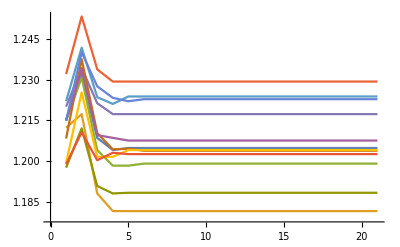

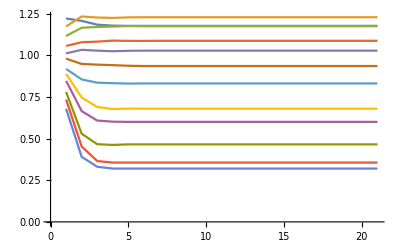

```mathematica
ListLinePlot[reddata3Dfixblue[0.33]]
ListLinePlot[yelldata3Dbluefix[0.33]]
```

```mathematica
ClearAll[yelldata3Dbluefix]
yelldata3Dbluefix[b_:0.5]:=Table[With[{maxSteps=Length[row[[2]]],colorProp=row[[1]]},Transpose[{Range[maxSteps],ConstantArray[colorProp,maxSteps],row[[2]]}]],{row,ParallelTable[With[{r=1-b-y},If[r==(1-b)/2&&y==(1-b)/2&&r+b+y>1,Nothing,{y,Mean/@Transpose[Table[Mean/@CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First@Commonest[neighbors],3],3,3},RandomChoice[Chop/@{b,r,y}->{2,1,0},200],20],30]]}]],{y,0.1,1-b,0.05}]}]
```

```mathematica
ClearAll[reddata3Dbluefix,y]
reddata3Dbluefix[b_:0.5]:=Table[With[{maxSteps=Length[row[[2]]],colorProp=row[[1]]},Transpose[{Range[maxSteps],ConstantArray[colorProp,maxSteps],row[[2]]}]],{row,ParallelTable[With[{y=1-b-r},If[r==(1-b)/2&&y==(1-b)/2&&r+b+y>1,Nothing,{r,Mean/@Transpose[Table[Mean/@CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First@Commonest[neighbors],3],3,3},RandomChoice[Chop/@{b,r,y}->{2,1,0},200],20],30]]}]],{r,0.1,1-b,0.05}]}]

Labeled[ListPlot3D[{Flatten[yelldata3Dbluefix[0.3],1],Flatten[reddata3Dfixblue[0.3],1]},PlotStyle-> {Yellow, Red}, ImageSize->Large, Ticks->{Range[1,22,2],Range[0.7,0.1,-0.1],Range[0.2,1.4,0.2]},AxesLabel-> {"Steps","Color Proportion","Color Tendency"}, LabelStyle -> Directive[Black, Bold]],"Fig 7"]
```

RandomChoice::wghtv: The weights given on the left-hand side of {0.3,0.7-y,y}→{2,1,0} should be a list of positive numerical quantities having the same length as the list given on the right-hand side.

Mean::rectt: Rectangular array expected at position 1 in Mean[20].

CellularAutomaton::rsize: The specified rule number 9706503538106178262918718548461843884716900015825131934815604616143786870493908755739676015379544915117876610861738417318683199400058231191192571190897801960952070997769368230295902922769316278028407088121534652337341867738604103172958550909067386298102952743891978574337167588618639746175563687989136381901591042799408600371826723681014824953590349260546223069345697954694216873713997087451983169100241476632389338634155870475148215829317493686226215540365633950901342305248197367473828626948«56»87201381137123455858051329767230889369597916295989554323136051186706808439351944706790299313195941847595791708503039021219001323949297129671383819599194082733369945243160338884561700299512670157849165643457944266555832105474035011651617800257731918006784728618532186564638075740079954786972256971490852749930964426988284793714673294247996780720970992331072636156755367996425577757218923224044038263747036766298109152663760400329906367763578847316459197017440680147092963557340978275033141868401 is greater than the largest possible rule number (255).

RandomChoice::wghtv: The weights given on the left-hand side of {0.3,0.7-y,y}→{2,1,0} should be a list of positive numerical quantities having the same length as the list given on the right-hand side.

Mean::rectt: Rectangular array expected at position 1 in Mean[20].

CellularAutomaton::rsize: The specified rule number 9706503538106178262918718548461843884716900015825131934815604616143786870493908755739676015379544915117876610861738417318683199400058231191192571190897801960952070997769368230295902922769316278028407088121534652337341867738604103172958550909067386298102952743891978574337167588618639746175563687989136381901591042799408600371826723681014824953590349260546223069345697954694216873713997087451983169100241476632389338634155870475148215829317493686226215540365633950901342305248197367473828626948«56»87201381137123455858051329767230889369597916295989554323136051186706808439351944706790299313195941847595791708503039021219001323949297129671383819599194082733369945243160338884561700299512670157849165643457944266555832105474035011651617800257731918006784728618532186564638075740079954786972256971490852749930964426988284793714673294247996780720970992331072636156755367996425577757218923224044038263747036766298109152663760400329906367763578847316459197017440680147092963557340978275033141868401 is greater than the largest possible rule number (255).

RandomChoice::wghtv: The weights given on the left-hand side of {0.3,0.7-y,y}→{2,1,0} should be a list of positive numerical quantities having the same length as the list given on the right-hand side.

General::stop: Further output of RandomChoice::wghtv will be suppressed during this calculation.

Mean::rectt: Rectangular array expected at position 1 in Mean[20].

General::stop: Further output of Mean::rectt will be suppressed during this calculation.

CellularAutomaton::rsize: The specified rule number 9706503538106178262918718548461843884716900015825131934815604616143786870493908755739676015379544915117876610861738417318683199400058231191192571190897801960952070997769368230295902922769316278028407088121534652337341867738604103172958550909067386298102952743891978574337167588618639746175563687989136381901591042799408600371826723681014824953590349260546223069345697954694216873713997087451983169100241476632389338634155870475148215829317493686226215540365633950901342305248197367473828626948«56»87201381137123455858051329767230889369597916295989554323136051186706808439351944706790299313195941847595791708503039021219001323949297129671383819599194082733369945243160338884561700299512670157849165643457944266555832105474035011651617800257731918006784728618532186564638075740079954786972256971490852749930964426988284793714673294247996780720970992331072636156755367996425577757218923224044038263747036766298109152663760400329906367763578847316459197017440680147092963557340978275033141868401 is greater than the largest possible rule number (255).

General::stop: Further output of CellularAutomaton::rsize will be suppressed during this calculation.

CellularAutomaton::nspecnl: Rule specification 9.706503538106178×10^1042 should be an Integer, a List, a pure Boolean function, a String, or an Association.

General::stop: Further output of CellularAutomaton::nspecnl will be suppressed during this calculation.

```mathematica
reddata3Dbluefix[b_:0.5]:=Table[With[{maxSteps=Length[row[[2]]],colorProp=row[[1]]},Transpose[{Range[maxSteps],ConstantArray[colorProp,maxSteps],row[[2]]}]],{row,ParallelTable[With[{y=1-b-r},If[r==(1-b)/2&&y==(1-b)/2&&r+b+y>1,Nothing,{r,Mean/@Transpose[Table[Mean/@CellularAutomaton[{FromDigits[Tuples[{2,1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First@Commonest[neighbors],3],3,3},RandomChoice[Chop/@{b,r,y}->{2,1,0},200],20],30]]}]],{r,0.1,1-b,0.05}]}]
```

```mathematica
reddata3Dbluefix[0.3]
```

{{{1,0.1,839/1200},{2,0.1,31/80},{3,0.1,1741/6000},{4,0.1,413/1500},{5,0.1,823/3000},{6,0.1,823/3000},{7,0.1,823/3000},{8,0.1,823/3000},{9,0.1,823/3000},{10,0.1,823/3000},{11,0.1,823/3000},{12,0.1,823/3000},{13,0.1,823/3000},{14,0.1,823/3000},{15,0.1,823/3000},{16,0.1,823/3000},{17,0.1,823/3000},{18,0.1,823/3000},{19,0.1,823/3000},{20,0.1,823/3000},{21,0.1,823/3000}},{{1,0.15,2197/3000},{2,0.15,2609/6000},{3,0.15,171/500},{4,0.15,1997/6000},{5,0.15,663/2000},{6,0.15,663/2000},{7,0.15,663/2000},{8,0.15,663/2000},{9,0.15,663/2000},{10,0.15,663/2000},{11,0.15,663/2000},{12,0.15,663/2000},{13,0.15,663/2000},{14,0.15,663/2000},{15,0.15,663/2000},{16,0.15,663/2000},{17,0.15,663/2000},{18,0.15,663/2000},{19,0.15,663/2000},{20,0.15,663/2000},{21,0.15,663/2000}},{{1,0.2,4859/6000},{2,0.2,701/1200},{3,0.2,51/100},{4,0.2,1487/3000},{5,0.2,987/2000},{6,0.2,987/2000},{7,0.2,987/2000},{8,0.2,987/2000},{9,0.2,987/2000},{10,0.2,987/2000},{11,0.2,987/2000},{12,0.2,987/2000},{13,0.2,987/2000},{14,0.2,987/2000},{15,0.2,987/2000},{16,0.2,987/2000},{17,0.2,987/2000},{18,0.2,987/2000},{19,0.2,987/2000},{20,0.2,987/2000},{21,0.2,987/2000}},{{1,0.25,511/600},{2,0.25,1037/1500},{3,0.25,1859/3000},{4,0.25,3593/6000},{5,0.25,3569/6000},{6,0.25,1783/3000},{7,0.25,1783/3000},{8,0.25,1783/3000},{9,0.25,1783/3000},{10,0.25,1783/3000},{11,0.25,1783/3000},{12,0.25,1783/3000},{13,0.25,1783/3000},{14,0.25,1783/3000},{15,0.25,1783/3000},{16,0.25,1783/3000},{17,0.25,1783/3000},{18,0.25,1783/3000},{19,0.25,1783/3000},{20,0.25,1783/3000},{21,0.25,1783/3000}},{{1,0.3,5323/6000},{2,0.3,4771/6000},{3,0.3,2281/3000},{4,0.3,377/500},{5,0.3,1127/1500},{6,0.3,281/375},{7,0.3,281/375},{8,0.3,281/375},{9,0.3,281/375},{10,0.3,281/375},{11,0.3,281/375},{12,0.3,281/375},{13,0.3,281/375},{14,0.3,281/375},{15,0.3,281/375},{16,0.3,281/375},{17,0.3,281/375},{18,0.3,281/375},{19,0.3,281/375},{20,0.3,281/375},{21,0.3,281/375}},{{1,0.35,5653/6000},{2,0.35,223/250},{3,0.35,1743/2000},{4,0.35,649/750},{5,0.35,5197/6000},{6,0.35,5197/6000},{7,0.35,5197/6000},{8,0.35,5197/6000},{9,0.35,5197/6000},{10,0.35,5197/6000},{11,0.35,5197/6000},{12,0.35,5197/6000},{13,0.35,5197/6000},{14,0.35,5197/6000},{15,0.35,5197/6000},{16,0.35,5197/6000},{17,0.35,5197/6000},{18,0.35,5197/6000},{19,0.35,5197/6000},{20,0.35,5197/6000},{21,0.35,5197/6000}},{{1,0.4,241/240},{2,0.4,767/750},{3,0.4,2067/2000},{4,0.4,3113/3000},{5,0.4,1247/1200},{6,0.4,623/600},{7,0.4,6227/6000},{8,0.4,6227/6000},{9,0.4,6227/6000},{10,0.4,6227/6000},{11,0.4,6227/6000},{12,0.4,6227/6000},{13,0.4,6227/6000},{14,0.4,6227/6000},{15,0.4,6227/6000},{16,0.4,6227/6000},{17,0.4,6227/6000},{18,0.4,6227/6000},{19,0.4,6227/6000},{20,0.4,6227/6000},{21,0.4,6227/6000}},{{1,0.45,6247/6000},{2,0.45,6401/6000},{3,0.45,397/375},{4,0.45,2113/2000},{5,0.45,1267/1200},{6,0.45,6341/6000},{7,0.45,6341/6000},{8,0.45,6341/6000},{9,0.45,6341/6000},{10,0.45,6341/6000},{11,0.45,6341/6000},{12,0.45,6341/6000},{13,0.45,6341/6000},{14,0.45,6341/6000},{15,0.45,6341/6000},{16,0.45,6341/6000},{17,0.45,6341/6000},{18,0.45,6341/6000},{19,0.45,6341/6000},{20,0.45,6341/6000},{21,0.45,6341/6000}},{{1,0.5,6581/6000},{2,0.5,851/750},{3,0.5,57/50},{4,0.5,6839/6000},{5,0.5,137/120},{6,0.5,6851/6000},{7,0.5,428/375},{8,0.5,428/375},{9,0.5,428/375},{10,0.5,428/375},{11,0.5,428/375},{12,0.5,428/375},{13,0.5,428/375},{14,0.5,428/375},{15,0.5,428/375},{16,0.5,428/375},{17,0.5,428/375},{18,0.5,428/375},{19,0.5,428/375},{20,0.5,428/375},{21,0.5,428/375}},{{1,0.55,2293/2000},{2,0.55,3479/3000},{3,0.55,2269/2000},{4,0.55,847/750},{5,0.55,271/240},{6,0.55,271/240},{7,0.55,271/240},{8,0.55,271/240},{9,0.55,271/240},{10,0.55,271/240},{11,0.55,271/240},{12,0.55,271/240},{13,0.55,271/240},{14,0.55,271/240},{15,0.55,271/240},{16,0.55,271/240},{17,0.55,271/240},{18,0.55,271/240},{19,0.55,271/240},{20,0.55,271/240},{21,0.55,271/240}},{{1,0.6,452/375},{2,0.6,883/750},{3,0.6,6899/6000},{4,0.6,6877/6000},{5,0.6,573/500},{6,0.6,2291/2000},{7,0.6,2291/2000},{8,0.6,2291/2000},{9,0.6,2291/2000},{10,0.6,2291/2000},{11,0.6,2291/2000},{12,0.6,2291/2000},{13,0.6,2291/2000},{14,0.6,2291/2000},{15,0.6,2291/2000},{16,0.6,2291/2000},{17,0.6,2291/2000},{18,0.6,2291/2000},{19,0.6,2291/2000},{20,0.6,2291/2000},{21,0.6,2291/2000}},{{1,0.65,3727/3000},{2,0.65,6883/6000},{3,0.65,3331/3000},{4,0.65,6619/6000},{5,0.65,3307/3000},{6,0.65,3307/3000},{7,0.65,3307/3000},{8,0.65,3307/3000},{9,0.65,3307/3000},{10,0.65,3307/3000},{11,0.65,3307/3000},{12,0.65,3307/3000},{13,0.65,3307/3000},{14,0.65,3307/3000},{15,0.65,3307/3000},{16,0.65,3307/3000},{17,0.65,3307/3000},{18,0.65,3307/3000},{19,0.65,3307/3000},{20,0.65,3307/3000},{21,0.65,3307/3000}},{{1,0.7,2593/2000},{2,0.7,449/400},{3,0.7,263/240},{4,0.7,2187/2000},{5,0.7,2187/2000},{6,0.7,2187/2000},{7,0.7,2187/2000},{8,0.7,2187/2000},{9,0.7,2187/2000},{10,0.7,2187/2000},{11,0.7,2187/2000},{12,0.7,2187/2000},{13,0.7,2187/2000},{14,0.7,2187/2000},{15,0.7,2187/2000},{16,0.7,2187/2000},{17,0.7,2187/2000},{18,0.7,2187/2000},{19,0.7,2187/2000},{20,0.7,2187/2000},{21,0.7,2187/2000}}}

```mathematica
Labeled[ListPlot3D[{Flatten[yelldata3Dbluefix[0.3],1],Flatten[reddata3Dbluefix[0.3],1]},PlotStyle-> {Yellow, Red}, ImageSize->Large, Ticks->{Range[1,22,2],Range[0.7,0.1,-0.1],Range[0.2,1.4,0.2]},AxesLabel-> {"Steps","Color Proportion","Color Tendency"}, LabelStyle -> Directive[Black, Bold]],"Fig 7"]
```

-Graphics3D-Fig 7

```mathematica
reddata3Dbluefix[0.3]
```

{{{1,0.583008,7073/6000},{2,0.583008,3499/3000},{3,0.583008,2279/2000},{4,0.583008,851/750},{5,0.583008,851/750},{6,0.583008,851/750},{7,0.583008,851/750},{8,0.583008,851/750},{9,0.583008,851/750},{10,0.583008,851/750},{11,0.583008,851/750},{12,0.583008,851/750},{13,0.583008,851/750},{14,0.583008,851/750},{15,0.583008,851/750},{16,0.583008,851/750},{17,0.583008,851/750},{18,0.583008,851/750},{19,0.583008,851/750},{20,0.583008,851/750},{21,0.583008,851/750}},{{1,0.583008,3529/3000},{2,0.583008,1177/1000},{3,0.583008,1381/1200},{4,0.583008,573/500},{5,0.583008,1717/1500},{6,0.583008,1717/1500},{7,0.583008,1717/1500},{8,0.583008,1717/1500},{9,0.583008,1717/1500},{10,0.583008,1717/1500},{11,0.583008,1717/1500},{12,0.583008,1717/1500},{13,0.583008,1717/1500},{14,0.583008,1717/1500},{15,0.583008,1717/1500},{16,0.583008,1717/1500},{17,0.583008,1717/1500},{18,0.583008,1717/1500},{19,0.583008,1717/1500},{20,0.583008,1717/1500},{21,0.583008,1717/1500}},{{1,0.583008,591/500},{2,0.583008,7049/6000},{3,0.583008,1721/1500},{4,0.583008,857/750},{5,0.583008,2283/2000},{6,0.583008,2283/2000},{7,0.583008,2283/2000},{8,0.583008,2283/2000},{9,0.583008,2283/2000},{10,0.583008,2283/2000},{11,0.583008,2283/2000},{12,0.583008,2283/2000},{13,0.583008,2283/2000},{14,0.583008,2283/2000},{15,0.583008,2283/2000},{16,0.583008,2283/2000},{17,0.583008,2283/2000},{18,0.583008,2283/2000},{19,0.583008,2283/2000},{20,0.583008,2283/2000},{21,0.583008,2283/2000}},{{1,0.583008,713/600},{2,0.583008,1409/1200},{3,0.583008,3451/3000},{4,0.583008,6859/6000},{5,0.583008,6869/6000},{6,0.583008,6869/6000},{7,0.583008,6869/6000},{8,0.583008,6869/6000},{9,0.583008,6869/6000},{10,0.583008,6869/6000},{11,0.583008,6869/6000},{12,0.583008,6869/6000},{13,0.583008,6869/6000},{14,0.583008,6869/6000},{15,0.583008,6869/6000},{16,0.583008,6869/6000},{17,0.583008,6869/6000},{18,0.583008,6869/6000},{19,0.583008,6869/6000},{20,0.583008,6869/6000},{21,0.583008,6869/6000}},{{1,0.583008,7091/6000},{2,0.583008,3541/3000},{3,0.583008,2307/2000},{4,0.583008,143/125},{5,0.583008,2289/2000},{6,0.583008,2289/2000},{7,0.583008,2289/2000},{8,0.583008,2289/2000},{9,0.583008,2289/2000},{10,0.583008,2289/2000},{11,0.583008,2289/2000},{12,0.583008,2289/2000},{13,0.583008,2289/2000},{14,0.583008,2289/2000},{15,0.583008,2289/2000},{16,0.583008,2289/2000},{17,0.583008,2289/2000},{18,0.583008,2289/2000},{19,0.583008,2289/2000},{20,0.583008,2289/2000},{21,0.583008,2289/2000}},{{1,0.583008,239/200},{2,0.583008,446/375},{3,0.583008,3503/3000},{4,0.583008,6973/6000},{5,0.583008,6967/6000},{6,0.583008,6967/6000},{7,0.583008,6967/6000},{8,0.583008,6967/6000},{9,0.583008,6967/6000},{10,0.583008,6967/6000},{11,0.583008,6967/6000},{12,0.583008,6967/6000},{13,0.583008,6967/6000},{14,0.583008,6967/6000},{15,0.583008,6967/6000},{16,0.583008,6967/6000},{17,0.583008,6967/6000},{18,0.583008,6967/6000},{19,0.583008,6967/6000},{20,0.583008,6967/6000},{21,0.583008,6967/6000}},{{1,0.583008,893/750},{2,0.583008,3557/3000},{3,0.583008,1739/1500},{4,0.583008,3467/3000},{5,0.583008,6941/6000},{6,0.583008,6941/6000},{7,0.583008,6941/6000},{8,0.583008,6941/6000},{9,0.583008,6941/6000},{10,0.583008,6941/6000},{11,0.583008,6941/6000},{12,0.583008,6941/6000},{13,0.583008,6941/6000},{14,0.583008,6941/6000},{15,0.583008,6941/6000},{16,0.583008,6941/6000},{17,0.583008,6941/6000},{18,0.583008,6941/6000},{19,0.583008,6941/6000},{20,0.583008,6941/6000},{21,0.583008,6941/6000}},{{1,0.583008,439/375},{2,0.583008,1161/1000},{3,0.583008,679/600},{4,0.583008,1349/1200},{5,0.583008,9/8},{6,0.583008,1687/1500},{7,0.583008,6751/6000},{8,0.583008,6751/6000},{9,0.583008,6751/6000},{10,0.583008,6751/6000},{11,0.583008,6751/6000},{12,0.583008,6751/6000},{13,0.583008,6751/6000},{14,0.583008,6751/6000},{15,0.583008,6751/6000},{16,0.583008,6751/6000},{17,0.583008,6751/6000},{18,0.583008,6751/6000},{19,0.583008,6751/6000},{20,0.583008,6751/6000},{21,0.583008,6751/6000}},{{1,0.583008,2359/2000},{2,0.583008,7069/6000},{3,0.583008,1151/1000},{4,0.583008,6883/6000},{5,0.583008,6883/6000},{6,0.583008,6883/6000},{7,0.583008,6883/6000},{8,0.583008,6883/6000},{9,0.583008,6883/6000},{10,0.583008,6883/6000},{11,0.583008,6883/6000},{12,0.583008,6883/6000},{13,0.583008,6883/6000},{14,0.583008,6883/6000},{15,0.583008,6883/6000},{16,0.583008,6883/6000},{17,0.583008,6883/6000},{18,0.583008,6883/6000},{19,0.583008,6883/6000},{20,0.583008,6883/6000},{21,0.583008,6883/6000}},{{1,0.583008,47/40},{2,0.583008,1177/1000},{3,0.583008,289/250},{4,0.583008,691/600},{5,0.583008,863/750},{6,0.583008,863/750},{7,0.583008,863/750},{8,0.583008,863/750},{9,0.583008,863/750},{10,0.583008,863/750},{11,0.583008,863/750},{12,0.583008,863/750},{13,0.583008,863/750},{14,0.583008,863/750},{15,0.583008,863/750},{16,0.583008,863/750},{17,0.583008,863/750},{18,0.583008,863/750},{19,0.583008,863/750},{20,0.583008,863/750},{21,0.583008,863/750}},{{1,0.583008,239/200},{2,0.583008,7103/6000},{3,0.583008,3467/3000},{4,0.583008,3443/3000},{5,0.583008,1723/1500},{6,0.583008,1723/1500},{7,0.583008,1723/1500},{8,0.583008,1723/1500},{9,0.583008,1723/1500},{10,0.583008,1723/1500},{11,0.583008,1723/1500},{12,0.583008,1723/1500},{13,0.583008,1723/1500},{14,0.583008,1723/1500},{15,0.583008,1723/1500},{16,0.583008,1723/1500},{17,0.583008,1723/1500},{18,0.583008,1723/1500},{19,0.583008,1723/1500},{20,0.583008,1723/1500},{21,0.583008,1723/1500}},{{1,0.583008,7123/6000},{2,0.583008,3539/3000},{3,0.583008,1391/1200},{4,0.583008,6929/6000},{5,0.583008,1733/1500},{6,0.583008,1733/1500},{7,0.583008,1733/1500},{8,0.583008,1733/1500},{9,0.583008,1733/1500},{10,0.583008,1733/1500},{11,0.583008,1733/1500},{12,0.583008,1733/1500},{13,0.583008,1733/1500},{14,0.583008,1733/1500},{15,0.583008,1733/1500},{16,0.583008,1733/1500},{17,0.583008,1733/1500},{18,0.583008,1733/1500},{19,0.583008,1733/1500},{20,0.583008,1733/1500},{21,0.583008,1733/1500}},{{1,0.583008,3539/3000},{2,0.583008,146/125},{3,0.583008,3413/3000},{4,0.583008,1699/1500},{5,0.583008,3401/3000},{6,0.583008,3401/3000},{7,0.583008,3401/3000},{8,0.583008,3401/3000},{9,0.583008,3401/3000},{10,0.583008,3401/3000},{11,0.583008,3401/3000},{12,0.583008,3401/3000},{13,0.583008,3401/3000},{14,0.583008,3401/3000},{15,0.583008,3401/3000},{16,0.583008,3401/3000},{17,0.583008,3401/3000},{18,0.583008,3401/3000},{19,0.583008,3401/3000},{20,0.583008,3401/3000},{21,0.583008,3401/3000}}}

```mathematica
Labeled[ListPlot3D[{yelldata3Dbluefix[0.3],reddata3Dfixblue[0.3]},PlotStyle-> {Yellow, Red}, ImageSize->Large, Ticks->{Range[1,22,2],Range[0.7,0.1,-0.1],Range[0.2,1.4,0.2]},AxesLabel-> {"Steps","Color Proportion","Color Tendency"}, LabelStyle -> Directive[Black, Bold]],"Fig 7"]
```

-Graphics3D-Fig 7

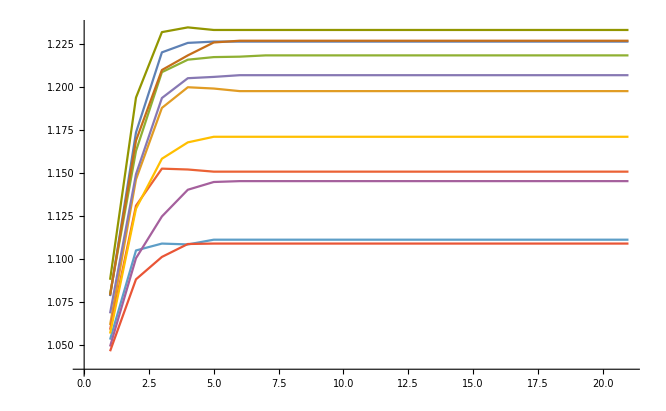

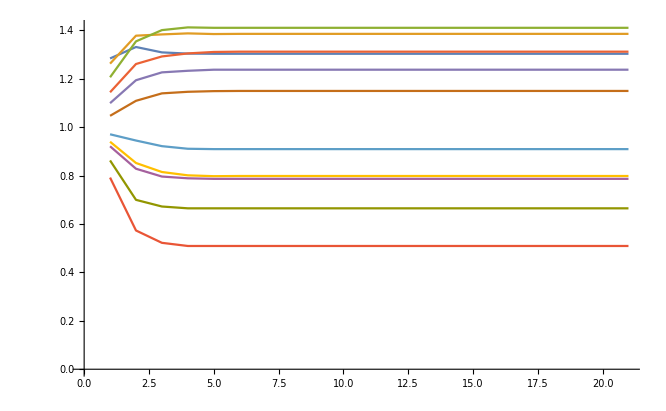

```mathematica
ListLinePlot[reddata]
ListLinePlot[yelldata]
```

```mathematica
data3D = ParallelTable[If[r==1/3 && y==1/3 && b==1/3 && r+y+b > 1 ,Nothing,Mean/@Transpose[Table[Mean/@CellularAutomaton[{FromDigits[Tuples[{1,0},7]/. neighbors:{l3_,b3_,l1_,c_,r1_,b1_,r3_}:>First @ Commonest[neighbors],3],3,3},RandomChoice[{r,y=1-r, b = 1-r- y}->{2,1,0},1000],20],20]]],{r,.3,.7,.05}];
data3D
```

{{{{651/500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{6479/5000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{13021/10000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{25997/20000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3259/2500,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{25921/20000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{25971/20000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{13021/10000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{2599/2000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},8},8}
 |  |  |  |

```mathematica
plotbehav3D[dat_]=ListLinePlot3D[MapThread[Callout[#1,Row[{Style["p",Italic],"=",#2}]]&,{dat_,Cases[Range[.3,.7,.05],Except[0.3]]}]];
```

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Callout[#1,p]&,{{«1»},{0.3,0.35,0.4,0.45,0.55,0.6,0.65,0.7}}]; dimensions are 9 and 8.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Callout[#1,p]&,{{{{{1.29585,0,0,0,0,0,0,0,0,0,«11»},{1.29925,0,0,0,0,0,0,0,0,0,«11»},{1.29435,0,0,0,0,0,0,0,0,0,«11»},{1.29745,0,0,0,0,0,0,0,0,0,«11»},{1.29805,0,0,0,0,0,0,0,0,0,«11»},{1.29635,0,0,0,0,0,0,0,0,0,«11»},{1.3001,0,0,0,0,0,0,0,0,0,«11»},{1.29925,0,0,0,0,0,0,0,0,0,«11»},{1.29825,0,0,0,0,0,0,0,0,0,«11»}},«7»,{{1.30325,0,0,0,0,0,0,0,0,0,«11»},{1.29795,0,0,0,0,0,0,0,0,0,«11»},«6»,{1.2998,0,0,0,0,0,0,0,0,0,«11»}}},«7»,{«1»}},«1»}]; dimensions are 9 and 8.

MapThread::mptc: Incompatible dimensions of objects at positions {2, 1} and {2, 2} of MapThread[Callout[#1,p]&,{{{{{1.29585,0.,0.,0.,0.,0.,0.,0.,0.,0.,«11»},{1.29925,0.,0.,0.,0.,0.,0.,0.,0.,0.,«11»},{1.29435,0.,0.,0.,0.,0.,0.,0.,0.,0.,«11»},{1.29745,0.,0.,0.,0.,0.,0.,0.,0.,0.,«11»},{1.29805,0.,0.,«5»,0.,0.,«11»},{1.29635,0.,0.,0.,0.,0.,0.,0.,0.,0.,«11»},{1.3001,0.,0.,0.,0.,0.,0.,0.,0.,0.,«11»},{1.29925,0.,0.,0.,0.,0.,0.,0.,0.,0.,«11»},{1.29825,0.,0.,0.,0.,0.,0.,0.,0.,0.,«11»}},«8»},«8»},«1»}]; dimensions are 9 and 8.

General::stop: Further output of MapThread::mptc will be suppressed during this calculation.

MapThread::list: List expected at position 2 in MapThread[1,2].

ListLinePlot3D::ldata: MapThread[Callout[#1,p]&,{{«1»},{0.3,0.35,0.4,0.45,0.55,0.6,0.65,0.7}}] is not a valid dataset or list of datasets.

ListLinePlot3D[MapThread[Callout[#1,p=#2]&,{{1},{0.3,0.35,0.4,0.45,0.55,0.6,0.65,0.7}}]]
 |  |  |  |